# The Tuner Circuit of NMR

```mathematica
(* the total impedance of the Detector unit *)
1/ZL=1/(ⅈ ω L￿+ 1/(ⅈ ω C1))+ⅈ ω (C0+C2)
```

```mathematica
1/(1/(ⅈ ω L+ 1/(ⅈ ω C1))+ⅈ ω (C0+C2))//FullSimplify
```

-ⅈ/(ω (C0+C2+C1/(1-C1 L ω^2)))

```mathematica
ZL[ω_,C0_,L_,C1_,C2_]:=1/(ω (C0+C2+C1/(1-C1  L ω^2)))
```

```mathematica
Manipulate[Plot[ZL[ω 10^6,2.2  10^-12,l 10^-6 ,C1 10^-12,C2 10^-12],{ω,3,20}],{l,1,10^6},{C1,0.1,10},{C2,0.1,10}]
```

```mathematica
Manipulate[1/((12.8 10^6)^2 C2 10^-12) 10^12,{C2,0.1,1000}]
```

```mathematica
Vin[ω_,C0_,L_,C1_,C2_]:=1-(ZL[ω,C0,L,C1,C2]-50)/(ZL[ω,C0,L,C1,C2]+50)
```

```mathematica
Manipulate[Plot[Vin[ω 10^6,2.2 10^-12,l 10^-6 ,C1 10^-12,C2 10^-12],{ω,3,20},PlotRange->{0,1}],{l,1,10^6},{C1,0.1,1000},{C2,0.1,1000}]
```

```mathematica
ⅈ ω Cs+1/(ⅈ ω (Cp+C0)+1/(ⅈ ω L))//FullSimplify
```

ⅈ ω (Cs-L/(-1+(C0+Cp) L ω^2))

```mathematica
Clear[ZL2]
```

```mathematica
ZL2[ω_,C0_,L_,Cs_,Cp_]:= ω (Cs-L/(-1+(C0+Cp) L ω^2))
```

```mathematica
Manipulate[Plot[ZL2[2π ω 10^6,2.2  10^-12,l 10^-6 ,Cs 10^-12,Cp 10^-12],{ω,3,20}],{l,1,10},{Cs,0.1,10},{Cp,0.1,10}]
```

```mathematica
Vin2[ω_,C0_,L_,Cs_,Cp_]:=1-(ZL2[ω,C0,L,Cs,Cp]-50)/(ZL2[ω,C0,L,Cs,Cp]+50)
```

```mathematica
Manipulate[Plot[Abs[Vin2[2π f 10^6,2.2 10^-12,l 10^-6 ,Cs 10^-6,Cp 10^-12]],{f,3,20},PlotRange->{0,2}],{l,1,10},{Cs,0.1,10},{Cp,0.1,1000}]
```

```mathematica
(* if we add little resistance *)
ZL[ω_,C0_,L_,Cs_,Cp_,Rs_,Rp_]:= √((Rs+(C0^2 L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(2 C0 Cp L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(Cp^2 L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2))^2+(Cs ω+(L ω)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)-(C0 L^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)-(Cp L^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(C0^2 L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(2 C0 Cp L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(Cp^2 L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2))^2)
```

```mathematica
Rs+ⅈ Cs ω+1/(1/(ⅈ ω L)+1/(Rp+1/(ⅈ ω (C0+Cp))))//FullSimplify
```

Rs+ⅈ Cs ω+(L ω (1+ⅈ (C0+Cp) Rp ω))/(-ⅈ+(C0+Cp) ω (Rp+ⅈ L ω))

```mathematica
ComplexExpand[Rs+ⅈ Cs ω+(L ω (1+ⅈ (C0+Cp) Rp ω))/(-ⅈ+(C0+Cp) ω (Rp+ⅈ L ω))]
```

Rs+(C0^2 L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(2 C0 Cp L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(Cp^2 L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+ⅈ (Cs ω+(L ω)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)-(C0 L^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)-(Cp L^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(C0^2 L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(2 C0 Cp L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(Cp^2 L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2))

```mathematica
√((Rs+(C0^2 L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(2 C0 Cp L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(Cp^2 L^2 Rp ω^4)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2))^2+(Cs ω+(L ω)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)-(C0 L^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)-(Cp L^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(C0^2 L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(2 C0 Cp L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2)+(Cp^2 L Rp^2 ω^3)/((C0+Cp)^2 Rp^2 ω^2+(-1+(C0+Cp) L ω^2)^2))^2)/.{Rs->0,Rp->0}//Simplify
```

√((ω^2 (L-Cs (-1+C0 L ω^2+Cp L ω^2))^2)/((-1+C0 L ω^2+Cp L ω^2)^2))

```mathematica
Vin3[ω_,C0_,L_,Cs_,Cp_,rs_,rp_]:=1-(ZL[ω,C0,L,Cs,Cp,rs,rp]-50)/(ZL[ω,C0,L,Cs,Cp,rs,rp]+50)
```

```mathematica
Manipulate[Plot[{Abs[Vin2[2π f 10^6,2.2 10^-12,l 10^-6 ,Cs 10^-12,Cp 10^-12]],Abs[Vin3[2π f 10^6,2.2 10^-12,l 10^-6 ,Cs 10^-12,Cp 10^-12,rs,rp]]},{f,3,15},PlotRange->{0,2}],{l,1,10},{Cs,0,1000},{Cp,0.1,1000},{rs,0,100},{rp,0,100}]
```

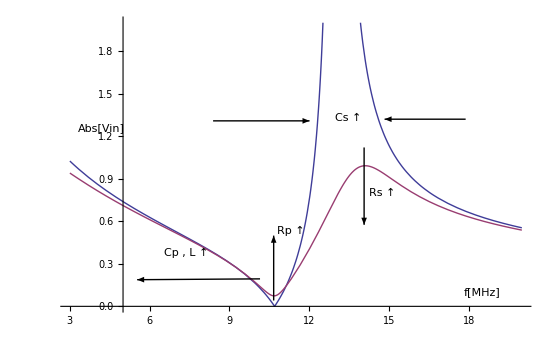

```mathematica
Solve[1-(ω (Cs-L/(-1+(C0+Cp) L ω^2))-50)/(ω (Cs-L/(-1+(C0+Cp) L ω^2))+50)==0,ω]//Simplify
```

{{ω→-1/(√((C0+Cp) L))},{ω→1/(√((C0+Cp) L))}}

```mathematica
(* V load *)
Vl[ω_,C0_,L_,Cs_,Cp_,rs_,rp_]:=Cos[2-(ZL[ω,C0,L,Cs,Cp,rs,rp]-50)/(ZL[ω,C0,L,Cs,Cp,rs,rp]+50)
```